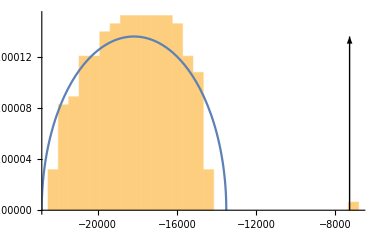

```mathematica
w1=NExpectation[z^2/Cosh[z]^2, z\[Distributed]NormalDistribution[]];
w2=NExpectation[1/Cosh[z]^2, z\[Distributed]NormalDistribution[]];

n=30000;
p=300;
β=Normalize@RandomVariate[NormalDistribution[], p];
X=RandomVariate[NormalDistribution[], {n, p}];
v = 1/Cosh[#.β]^2&/@X;
Hess=(-Transpose[X].DiagonalMatrix[v].X);

eigenHist=Histogram[Eigenvalues[Hess], {"Raw",30},"PDF"];

rad = 2Sqrt[n*p*w2];
cen=-n*w2;
eigenBulk=Plot[Sqrt[rad^2 - (s-cen)^2]/(Pi*rad^2/2), {s,cen-rad, cen+rad}];
eigenLonely=Graphics@Arrow[{{-n*w1, 0}, {-n*w1, 1/(Pi*rad/2)}}];

Show[eigenHist,eigenBulk, eigenLonely]
```

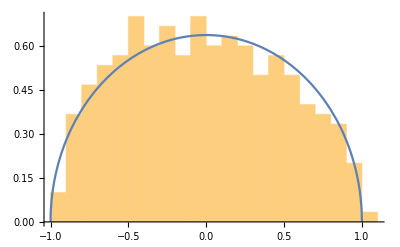

```mathematica
mu=NExpectation[1/Cosh[z]^2, z\[Distributed]NormalDistribution[]];
sig=Sqrt@NExpectation[1/Cosh[z]^4, z\[Distributed]NormalDistribution[]];

n=30000;
p=300;
X=RandomVariate[NormalDistribution[], {n, p}];
v = 1/Cosh[#]^2&/@RandomVariate[NormalDistribution[], n];
covMat=(Transpose[X].DiagonalMatrix[v].X - n*mu*IdentityMatrix[p])/(sig*2*Sqrt[n*p]);

covEigenHist = Histogram[Eigenvalues[covMat], 20,"PDF"];
semicircleLaw=Plot[2Sqrt[1-x^2]/Pi, {x, -1, 1}];

Show[covEigenHist, semicircleLaw]
```